## DEFINE PARAMETERS

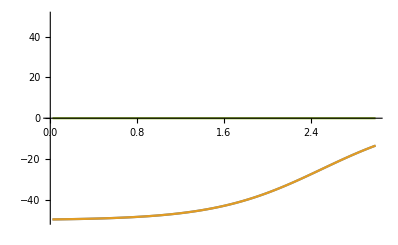

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=50;R=2.5;a=0.5;μ=8/9 Subscript[m, N];l=0;
rmax=3.;dr=0.02;ri=10^-100;
rlist=Range[ri,rmax,dr];
len=Length[rlist];
Vwoods[r_]:=-V0/(1+Exp[(r-R)/a]);
Vcent[r_]:=(l(l+1)ℏc^2)/(2μ r^2);
V[r_]:=-V0/(1+Exp[(r-R)/a])+(l(l+1)ℏc^2)/(2μ r^2);
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[{V[rlist],Vwoods[rlist],Vcent[rlist]},DataRange->{dr,rmax},PlotRange->{-V0,V0}]
```

```mathematica
(*INITIAL HAMILTONIAN*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H0:=Vmat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
```

## BOUND SOLUTIONS

```mathematica
(*BOUND SOLUTION*)
κ[En_]:=Sqrt[(2μ En)/ℏc^2];
wavebound[En_,r_,l_]:=r SphericalHankelH1[l,κ[En] r];
Bbound[En_,l_]:=rmax/wavebound[En,rmax,l](D[wavebound[En,r,l],r]/.r->rmax);
(*HAMILTONIAN*)
Hnewbound[En_,l_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bbound[En,l]/rmax-1);H);
(*RETURNS EIGENVALUE*)
eigenvbound[{En_,i_,l_}]:=({evalbound,evecbound}=Transpose@SortBy[Transpose[Eigensystem[Hnewbound[En,l]]],First];{evalbound[[i]],i,l})
```

```mathematica
ϵ=10^-10;
n=1;
evalsbound=List[];evecsbound=List[];
```

```mathematica
(*RETURNS EIGENSYSTEM*)
En=NestWhileList[eigenvbound,{-V0/2,n,l},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,100][[-1,1]];
While[Re[En]<0,
evalsbound=Append[evalsbound,En];
evecsbound=Append[evecsbound,evecbound[[n]]];
n++;
If[Re[eigenvbound[eigenvbound[{-V0/2,n,l}]][[1]]]<0,En=NestWhileList[eigenvbound,{-V0/2,n,l},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,100][[-1,1]];,En=1;]]
```

```mathematica
evalsbound
```

{-23.0975+0. ⅈ}

```mathematica
evalsbound
```

{-22.8935+0. ⅈ}

```mathematica
evalsbound(*rmax=10fm,V0=9MeV,dr=0.01*)
```

{}

```mathematica
evalsbound(*rmax=10fm,V0=8MeV,dr=0.01*)
```

{}

```mathematica
evalsbound(*rmax=20fm,V0=9MeV,dr=0.01fm*)
```

{-0.00758694+0. ⅈ}

```mathematica
evalsbound(*rmax=20fm,V0=9MeV,dr=0.02fm*)
```

{-0.00759041+0. ⅈ}

```mathematica
evalsbound(*rmax=20fm,V0=8MeV,dr=0.02fm*)
```

{}

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
constbound[i_]:=evecsbound[[i,-1]]/Abs[wavebound[evalsbound[[i]],rmax,l]];
rmaxx=10.;
normbound[i_]:=Module[{ψ=Interpolation[Transpose[{Flatten[Append[rlist,Range[rmax+dr,rmaxx,dr]]],Flatten[Append[evecsbound⟦i⟧,constbound[i] wavebound[evalsbound[[i]],Range[rmax+dr,rmaxx,dr],l]]]}]]},Sqrt[1/NIntegrate[Abs[ψ[x]]^2,{x,dr,rmaxx}]]]
```

```mathematica
evecsbound[[1]]
```

{0.00224527+0. ⅈ,0.0044895+0. ⅈ,0.00673167+0. ⅈ,0.00897075+0. ⅈ,0.0112057+0. ⅈ,0.0134355+0. ⅈ,0.0156592+0. ⅈ,0.0178757+0. ⅈ,0.020084+0. ⅈ,0.0222831+0. ⅈ,0.0244721+0. ⅈ,0.0266498+0. ⅈ,0.0288154+0. ⅈ,0.0309679+0. ⅈ,0.0331062+0. ⅈ,0.0352295+0. ⅈ,0.0373367+0. ⅈ,0.039427+0. ⅈ,0.0414994+0. ⅈ,0.0435529+0. ⅈ,0.0455867+0. ⅈ,0.0475999+0. ⅈ,0.0495915+0. ⅈ,0.0515608+0. ⅈ,0.0535068+0. ⅈ,0.0554287+0. ⅈ,0.0573256+0. ⅈ,0.0591968+0. ⅈ,0.0610415+0. ⅈ,0.0628588+0. ⅈ,0.064648+0. ⅈ,0.0664083+0. ⅈ,0.068139+0. ⅈ,0.0698394+0. ⅈ,0.0715087+0. ⅈ,0.0731464+0. ⅈ,0.0747517+0. ⅈ,0.0763239+0. ⅈ,0.0778626+0. ⅈ,0.079367+0. ⅈ,0.0808366+0. ⅈ,0.0822708+0. ⅈ,0.0836691+0. ⅈ,0.085031+0. ⅈ,0.086356+0. ⅈ,0.0876435+0. ⅈ,0.0888932+0. ⅈ,0.0901047+0. ⅈ,0.0912775+0. ⅈ,0.0924113+0. ⅈ,0.0935057+0. ⅈ,0.0945604+0. ⅈ,0.0955751+0. ⅈ,0.0965495+0. ⅈ,0.0974834+0. ⅈ,0.0983765+0. ⅈ,0.0992287+0. ⅈ,0.10004+0. ⅈ,0.10081+0. ⅈ,0.101538+0. ⅈ,0.102225+0. ⅈ,0.102871+0. ⅈ,0.103475+0. ⅈ,0.104037+0. ⅈ,0.104558+0. ⅈ,0.105038+0. ⅈ,0.105476+0. ⅈ,0.105873+0. ⅈ,0.106229+0. ⅈ,0.106543+0. ⅈ,0.106817+0. ⅈ,0.107051+0. ⅈ,0.107244+0. ⅈ,0.107397+0. ⅈ,0.10751+0. ⅈ,0.107584+0. ⅈ,0.107619+0. ⅈ,0.107615+0. ⅈ,0.107573+0. ⅈ,0.107493+0. ⅈ,0.107376+0. ⅈ,0.107222+0. ⅈ,0.107031+0. ⅈ,0.106805+0. ⅈ,0.106543+0. ⅈ,0.106247+0. ⅈ,0.105916+0. ⅈ,0.105552+0. ⅈ,0.105155+0. ⅈ,0.104726+0. ⅈ,0.104265+0. ⅈ,0.103774+0. ⅈ,0.103252+0. ⅈ,0.102701+0. ⅈ,0.102122+0. ⅈ,0.101515+0. ⅈ,0.10088+0. ⅈ,0.100219+0. ⅈ,0.0995333+0. ⅈ,0.0988224+0. ⅈ,0.0980878+0. ⅈ,0.0973301+0. ⅈ,0.0965503+0. ⅈ,0.0957491+0. ⅈ,0.0949275+0. ⅈ,0.0940863+0. ⅈ,0.0932264+0. ⅈ,0.0923485+0. ⅈ,0.0914537+0. ⅈ,0.0905427+0. ⅈ,0.0896164+0. ⅈ,0.0886756+0. ⅈ,0.0877212+0. ⅈ,0.0867541+0. ⅈ,0.0857751+0. ⅈ,0.0847851+0. ⅈ,0.0837847+0. ⅈ,0.082775+0. ⅈ,0.0817566+0. ⅈ,0.0807304+0. ⅈ,0.0796971+0. ⅈ,0.0786575+0. ⅈ,0.0776124+0. ⅈ,0.0765625+0. ⅈ,0.0755085+0. ⅈ,0.0744511+0. ⅈ,0.073391+0. ⅈ,0.0723289+0. ⅈ,0.0712655+0. ⅈ,0.0702013+0. ⅈ,0.0691369+0. ⅈ,0.068073+0. ⅈ,0.0670102+0. ⅈ,0.0659489+0. ⅈ,0.0648897+0. ⅈ,0.0638332+0. ⅈ,0.0627797+0. ⅈ,0.0617298+0. ⅈ,0.0606839+0. ⅈ,0.0596424+0. ⅈ,0.0586058+0. ⅈ,0.0575743+0. ⅈ,0.0565485+0. ⅈ,0.0555285+0. ⅈ,0.0545148+0. ⅈ,0.0535075+0. ⅈ,0.0525071+0. ⅈ,0.0515137+0. ⅈ,0.0505276+0. ⅈ,0.049549+0. ⅈ,0.0485781+0. ⅈ}

```mathematica
evecsbound[[1]]=Prepend[evecsbound[[1]],0.]
```

{0.,0.00224527+0. ⅈ,0.0044895+0. ⅈ,0.00673167+0. ⅈ,0.00897075+0. ⅈ,0.0112057+0. ⅈ,0.0134355+0. ⅈ,0.0156592+0. ⅈ,0.0178757+0. ⅈ,0.020084+0. ⅈ,0.0222831+0. ⅈ,0.0244721+0. ⅈ,0.0266498+0. ⅈ,0.0288154+0. ⅈ,0.0309679+0. ⅈ,0.0331062+0. ⅈ,0.0352295+0. ⅈ,0.0373367+0. ⅈ,0.039427+0. ⅈ,0.0414994+0. ⅈ,0.0435529+0. ⅈ,0.0455867+0. ⅈ,0.0475999+0. ⅈ,0.0495915+0. ⅈ,0.0515608+0. ⅈ,0.0535068+0. ⅈ,0.0554287+0. ⅈ,0.0573256+0. ⅈ,0.0591968+0. ⅈ,0.0610415+0. ⅈ,0.0628588+0. ⅈ,0.064648+0. ⅈ,0.0664083+0. ⅈ,0.068139+0. ⅈ,0.0698394+0. ⅈ,0.0715087+0. ⅈ,0.0731464+0. ⅈ,0.0747517+0. ⅈ,0.0763239+0. ⅈ,0.0778626+0. ⅈ,0.079367+0. ⅈ,0.0808366+0. ⅈ,0.0822708+0. ⅈ,0.0836691+0. ⅈ,0.085031+0. ⅈ,0.086356+0. ⅈ,0.0876435+0. ⅈ,0.0888932+0. ⅈ,0.0901047+0. ⅈ,0.0912775+0. ⅈ,0.0924113+0. ⅈ,0.0935057+0. ⅈ,0.0945604+0. ⅈ,0.0955751+0. ⅈ,0.0965495+0. ⅈ,0.0974834+0. ⅈ,0.0983765+0. ⅈ,0.0992287+0. ⅈ,0.10004+0. ⅈ,0.10081+0. ⅈ,0.101538+0. ⅈ,0.102225+0. ⅈ,0.102871+0. ⅈ,0.103475+0. ⅈ,0.104037+0. ⅈ,0.104558+0. ⅈ,0.105038+0. ⅈ,0.105476+0. ⅈ,0.105873+0. ⅈ,0.106229+0. ⅈ,0.106543+0. ⅈ,0.106817+0. ⅈ,0.107051+0. ⅈ,0.107244+0. ⅈ,0.107397+0. ⅈ,0.10751+0. ⅈ,0.107584+0. ⅈ,0.107619+0. ⅈ,0.107615+0. ⅈ,0.107573+0. ⅈ,0.107493+0. ⅈ,0.107376+0. ⅈ,0.107222+0. ⅈ,0.107031+0. ⅈ,0.106805+0. ⅈ,0.106543+0. ⅈ,0.106247+0. ⅈ,0.105916+0. ⅈ,0.105552+0. ⅈ,0.105155+0. ⅈ,0.104726+0. ⅈ,0.104265+0. ⅈ,0.103774+0. ⅈ,0.103252+0. ⅈ,0.102701+0. ⅈ,0.102122+0. ⅈ,0.101515+0. ⅈ,0.10088+0. ⅈ,0.100219+0. ⅈ,0.0995333+0. ⅈ,0.0988224+0. ⅈ,0.0980878+0. ⅈ,0.0973301+0. ⅈ,0.0965503+0. ⅈ,0.0957491+0. ⅈ,0.0949275+0. ⅈ,0.0940863+0. ⅈ,0.0932264+0. ⅈ,0.0923485+0. ⅈ,0.0914537+0. ⅈ,0.0905427+0. ⅈ,0.0896164+0. ⅈ,0.0886756+0. ⅈ,0.0877212+0. ⅈ,0.0867541+0. ⅈ,0.0857751+0. ⅈ,0.0847851+0. ⅈ,0.0837847+0. ⅈ,0.082775+0. ⅈ,0.0817566+0. ⅈ,0.0807304+0. ⅈ,0.0796971+0. ⅈ,0.0786575+0. ⅈ,0.0776124+0. ⅈ,0.0765625+0. ⅈ,0.0755085+0. ⅈ,0.0744511+0. ⅈ,0.073391+0. ⅈ,0.0723289+0. ⅈ,0.0712655+0. ⅈ,0.0702013+0. ⅈ,0.0691369+0. ⅈ,0.068073+0. ⅈ,0.0670102+0. ⅈ,0.0659489+0. ⅈ,0.0648897+0. ⅈ,0.0638332+0. ⅈ,0.0627797+0. ⅈ,0.0617298+0. ⅈ,0.0606839+0. ⅈ,0.0596424+0. ⅈ,0.0586058+0. ⅈ,0.0575743+0. ⅈ,0.0565485+0. ⅈ,0.0555285+0. ⅈ,0.0545148+0. ⅈ,0.0535075+0. ⅈ,0.0525071+0. ⅈ,0.0515137+0. ⅈ,0.0505276+0. ⅈ,0.049549+0. ⅈ,0.0485781+0. ⅈ}

```mathematica
rlist=Prepend[rlist,0.]
```

{0.,1.×10^-100,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5,0.52,0.54,0.56,0.58,0.6,0.62,0.64,0.66,0.68,0.7,0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1.,1.02,1.04,1.06,1.08,1.1,1.12,1.14,1.16,1.18,1.2,1.22,1.24,1.26,1.28,1.3,1.32,1.34,1.36,1.38,1.4,1.42,1.44,1.46,1.48,1.5,1.52,1.54,1.56,1.58,1.6,1.62,1.64,1.66,1.68,1.7,1.72,1.74,1.76,1.78,1.8,1.82,1.84,1.86,1.88,1.9,1.92,1.94,1.96,1.98,2.,2.02,2.04,2.06,2.08,2.1,2.12,2.14,2.16,2.18,2.2,2.22,2.24,2.26,2.28,2.3,2.32,2.34,2.36,2.38,2.4,2.42,2.44,2.46,2.48,2.5,2.52,2.54,2.56,2.58,2.6,2.62,2.64,2.66,2.68,2.7,2.72,2.74,2.76,2.78,2.8,2.82,2.84,2.86,2.88,2.9,2.92,2.94,2.96,2.98,3.}

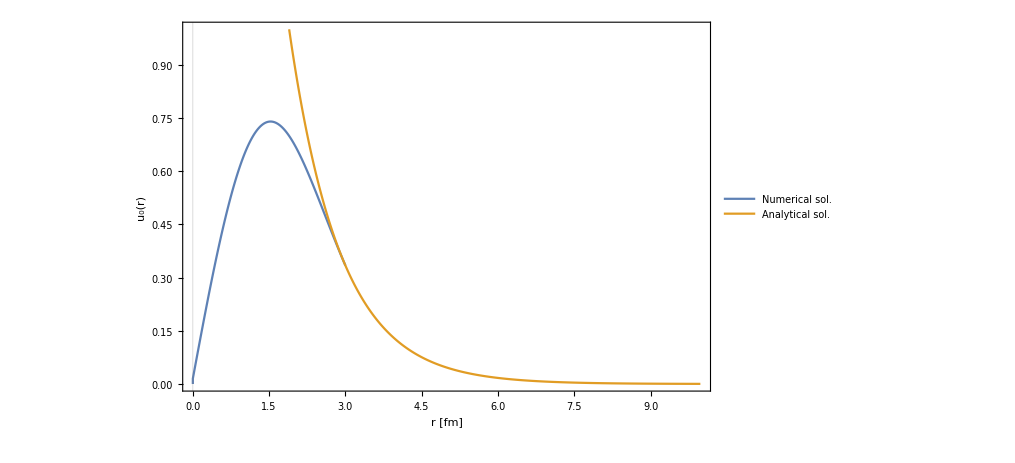

```mathematica
i=1;ListLinePlot[{Transpose[{rlist,normbound[i] evecsbound⟦i⟧}],Transpose[{Range[10^-10,rmaxx,dr],normbound[i]constbound[i]Abs[wavebound[evalsbound[[i]],Range[10^-10,rmaxx,dr],l]]}]},PlotRange->{0.,1.},FrameLabel->{Style["r [fm]",20,Black,FontFamily->"Asana Math"],Style["u_0(r)",20,Black,FontFamily->"Asana Math"]},Frame->True,PlotLegends->Placed[{Style["Numerical sol.",20,Black,FontFamily->"Asana Math"],Style["Analytical sol.",20,Black,FontFamily->"Asana Math"]},{0.7,0.65}],FrameTicksStyle->Directive[Black,12],GridLines->{{{0.,Gray}},None}]
```

```mathematica
.
```

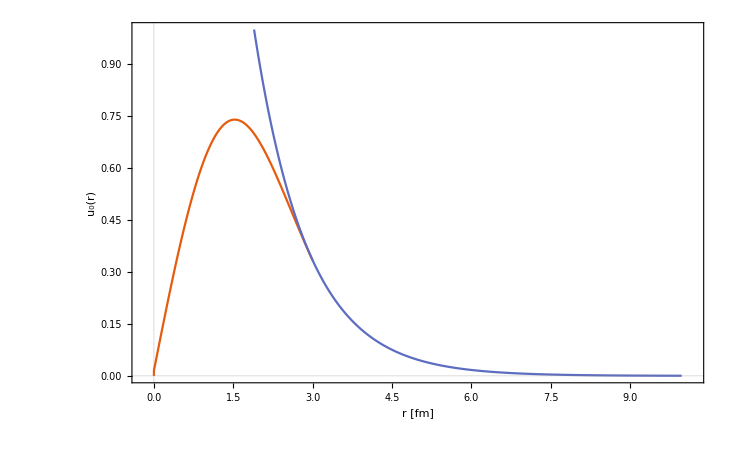

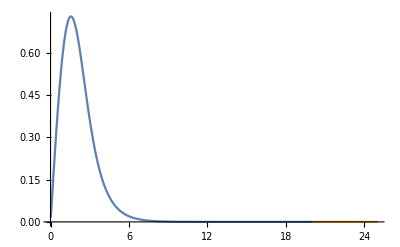

## RESONANCE STATES

```mathematica
(*RESONANCE SOLUTION*)
k[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
waveres[En_?NumericQ,r_,l_]:=SphericalHankelH1[l,k[En] r];
Bres[En_?NumericQ,l_]:=rmax/waveres[En,rmax,l](D[waveres[En,r,l],r]/.r->rmax);
(*HAMILTONIAN*)
Hnewres[En_?NumericQ,l_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bres[En,l]/rmax-1);H);
(*RETURNS EIGENVALUE*)
eigenvres[{En_?NumericQ,i_,l_}]:=({evalres,evecres}=Transpose@SortBy[Transpose[Eigensystem[Hnewres[En,l]]],First];{evalres[[i]],i,l})
(*eigenvres1[En_?NumericQ,i_,l_]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnewres[En,l]]],First];eval[[i]])*)
```

```mathematica
ϵ=10^-10;
n=1;
evalsres=List[];evecsres=List[];
```

```mathematica
(*RETURNS EIGENSYSTEM*)
(*En=x/.FindRoot[Im[eigenvres1[x,n,l]]==Im[x],{x,0.1+0.I,0.,V0}]//Timing*)
En=NestWhileList[eigenvres,{0,n,l},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,100][[-1,1]];
evalsres=Append[evalsres,En];evecsres=Append[evecsres,evecres[[n]]];
```

```mathematica
evalsres(*V0=8MeV,rmax=10fm,dr=0.01fm*)
```

{0.238353-0.216854 ⅈ}

```mathematica
evalsres(*V0=8MeV,rmax=20fm,dr=0.02fm*)
```

{0.0659602-0.0495609 ⅈ}

```mathematica
(*For[i=2,i≤5,i++,En=NestWhileList[eigenvres,{0,i,l},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,100][[-1,1]];
evalsres=Append[evalsres,En];
evecsres=Append[evecsres,evecres[[i]]];]*)
```

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
constres[i_]:=evecsres[[i,-1]]/waveres[evalsres[[i]],rmax,l];
rmaxx=50.;
```

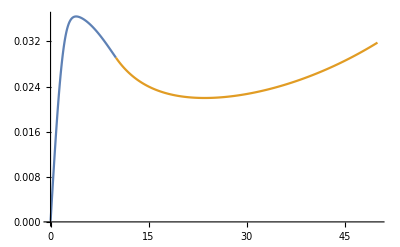

```mathematica
ListLinePlot[{Transpose[{rlist,Abs[evecsres⟦1⟧]}],Transpose[{Range[rmax,rmaxx,dr],Abs[constres[1] waveres[evalsres[[1]],Range[rmax,rmaxx,dr],l]]}]},PlotRange->All](*V0=8MeV,rmax=10fm,dr=0.01fm*)
```

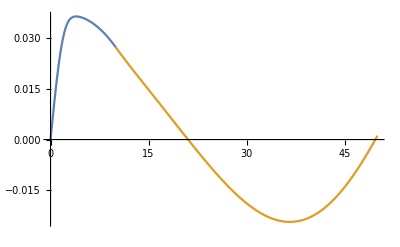

```mathematica
ListLinePlot[{Transpose[{rlist,Re[evecsres⟦1⟧]}],Transpose[{Range[rmax,rmaxx,dr],Re[constres[1] waveres[evalsres[[1]],Range[rmax,rmaxx,dr],l]]}]},PlotRange->All](*V0=8MeV,rmax=10fm,dr=0.01fm.....this grows exponentially with sinusoidal variation*)
```

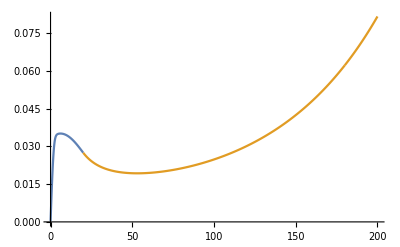

```mathematica
ListLinePlot[{Transpose[{rlist,Abs[evecsres⟦1⟧]}],Transpose[{Range[rmax,rmaxx,dr],Abs[constres[1] waveres[evalsres[[1]],Range[rmax,rmaxx,dr],l]]}]},PlotRange->All](*V0=8MeV,rmax=20fm,dr=0.02fm*)
```

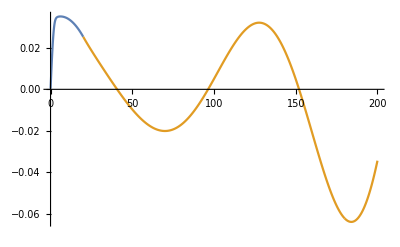

```mathematica
ListLinePlot[{Transpose[{rlist,Re[evecsres⟦1⟧]}],Transpose[{Range[rmax,rmaxx,dr],Re[constres[1] waveres[evalsres[[1]],Range[rmax,rmaxx,dr],l]]}]},PlotRange->All](*V0=8MeV,rmax=20fm,dr=0.02fm.....this grows exponentially with sinusoidal variation*)
```

## SCATTERING SOLUTIONS

```mathematica
(*SCATTERING SOLUTION*)
ks[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
wavescat[En_,r_,δ_,l_]:=1/2 Exp[I δ](Cos[δ]SphericalBesselJ[l,ks[En] r]-Sin[δ] SphericalBesselY[l,ks[En] r]);
(*Bscat[En_?NumericQ,δ_?NumericQ,l_]:=k[En] rmax(((Cos[δ] ∂_x SphericalBesselJ[l,x]/.x->k[En] rmax)-(Sin[δ] ∂_x SphericalBesselY[l,x]/.x->k[En] rmax))/(Cos[δ]SphericalBesselJ[l,k[En] rmax]-Sin[δ]SphericalBesselY[l,k[En] rmax]));*)
Bscat[En_?NumericQ,δ_?NumericQ,l_]:=rmax/wavescat[En,rmax,δ,l] D[wavescat[En,r,δ,l],r]/.{r->rmax};
(*HAMILTONIAN*)
Hnewscat[En_?NumericQ,δ_?NumericQ,l_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bscat[En,δ,l]/rmax-1);H);
(*RETURNS EIGEINVALUE*)
eigenvscat[En_?NumericQ,i_,δ_?NumericQ,l_]:=({evalscat,evecscat}=Transpose@SortBy[Transpose[Eigensystem[Hnewscat[En,δ,l]]],First];evalscat[[i]]);
(*FINDS ENERGY LEVEL AND PHASE*)
(*findnd[En_]:=Module[{phase=List[],n=1},(While[Max[Table[eigenvscat[{En,n,δ,l}][[1]],{δ,0.,π,0.01}]]<En,n++;];phase=Table[{eigenvscat[{En,n,δ,l}][[1]],δ},{δ,0,π,0.001}];δ=phase[[Position[phase[[All,1]],Nearest[phase[[All,1]],En][[1]]][[1,1]],2]];{n,δ})]*)
findnd[En_?NumericQ]:=Module[{n=1},While[Max[Table[eigenvscat[En,n,x,l],{x,0.,π,0.1}]]<En,n++;];δ=x/.FindRoot[eigenvscat[En,n,x,l]==En,{x,0.,-Pi,Pi}];If[δ<0,δ=π+δ];{n,δ}];
(*MATCHES AMPLITUDE*)
constscat[i_]:=evecscat[[i,-1]]/wavescat[evalscat[[i]],rmax,δ,l];
```

## PLOTS

{0.238535+0. ⅈ,1,0.456772+0. ⅈ}

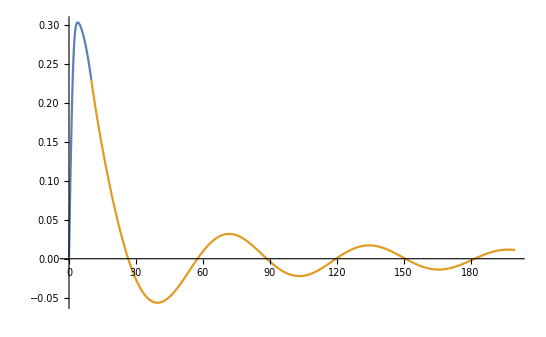

```mathematica
(*V0=10MeV,rmax=10fm,dr=0.01*)
rmaxx=200;
nd=findnd[0.238535];
Print[{evalscat[[n]],n,δ}];
ListLinePlot[{Transpose[{rlist,normscat[nd[[1]]] Re[evecscat⟦nd[[1]]⟧]}],Transpose[{Range[rmax,rmaxx,dr],normscat[nd[[1]]] Re[constscat[nd[[1]]] wavescat[evalscat[[nd[[1]]]],Range[rmax,rmaxx,dr],nd[[2]],l]]}]},PlotRange->All]
```

```mathematica
phasedata=Table[{x,findnd[x][[2]]},{x,0.9,2.0,0.1}];
```

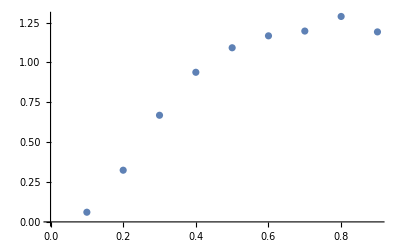

```mathematica
ListPlot[phasedata,GridLines->{None, {{Pi/2,Red}}}]
```

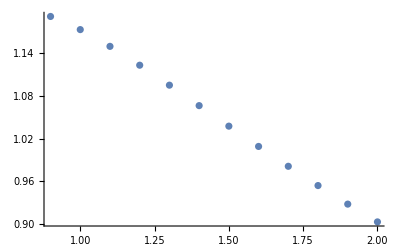

```mathematica
ListPlot[phasedata,GridLines->{None, {{Pi/2,Red}}}]
```

{0.0659602+0. ⅈ,1,0.492893+0. ⅈ}

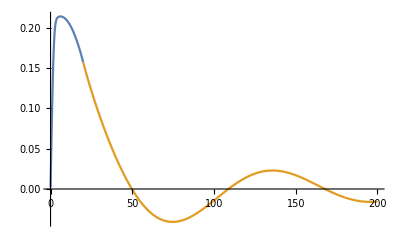

```mathematica
(*V0=10MeV,rmax=20fm,dr=0.02*)
rmaxx=200;
nd=findnd[0.0659602];
Print[{evalscat[[n]],n,δ}];
ListLinePlot[{Transpose[{rlist,normscat[nd[[1]]] Re[evecscat⟦nd[[1]]⟧]}],Transpose[{Range[rmax,rmaxx,dr],normscat[nd[[1]]] Re[constscat[nd[[1]]] wavescat[evalscat[[nd[[1]]]],Range[rmax,rmaxx,dr],nd[[2]],l]]}]},PlotRange->All]
```

```mathematica
phasedata=Table[{x,findnd[x][[2]]},{x,0.1,2.0,0.1}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

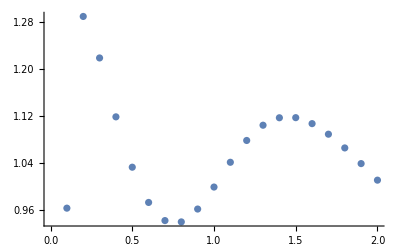

```mathematica
ListPlot[phasedata,GridLines->{None, {{Pi/2,Red}}}]
```